```mathematica
ClearAll["global`*"]
```

## Solution in external harmonic potential

```mathematica
M={{-(2*κ+k)/γ,0},{0,-k/γ}};
```

```mathematica
MatrixForm[M]
```

((-k-2 κ)/γ | 0
0 | -k/γ)

```mathematica
expM=MatrixExp[M*(t-tp)];
```

```mathematica
covar=Integrate[expM.{{4/γ^2*2*(Subscript[T, 1]+Subscript[T, 2])/2*γ/2,1/γ^2*2*(Subscript[T, 1]-Subscript[T, 2])*γ/2},{1/γ^2*2*(Subscript[T, 1]-Subscript[T, 2])*γ/2,1/(4*γ^2)*2*(Subscript[T, 1]+Subscript[T, 2])/2*2*γ}}.Transpose[expM],{tp,-Infinity,t},Assumptions->{γ>0,k>0,κ>0}];
```

```mathematica
P[R_,r_,kk_]:=Simplify[Exp[-1/2*{r,R}.Inverse[covar].{r,R}]]/.{k->kk}
```

## Patching and normalization

```mathematica
SubMinus[k]=2*Subscript[U, 0]/L^2;
```

```mathematica
SubPlus[k]=2*Subscript[U, 0]/l^2;
```

```mathematica
SubMinus[f]=Integrate[P[R,r,SubMinus[k]],{r,-Infinity,Infinity},Assumptions->{γ>0,κ>0,Subscript[U, 0]>0,l>0,L>0,Subscript[T, 1]>0,Subscript[T, 2]>0}];
```

```mathematica
SubPlus[f]=Integrate[P[R,r,SubPlus[k]],{r,-Infinity,Infinity},Assumptions->{γ>0,κ>0,Subscript[U, 0]>0,l>0,L>0,Subscript[T, 1]>0,Subscript[T, 2]>0}];
```

```mathematica
{{SubMinus[exprA],SubPlus[exprA]}}=Simplify[Solve[SubMinus[A]*(SubMinus[f]/.{R->0})==SubPlus[A]*(SubPlus[f]/.{R->0})&&SubMinus[A]*Integrate[SubMinus[f],{R,-L,0},Assumptions->{γ>0,κ>0,Subscript[U, 0]>0,l>0,L>0,Subscript[T, 1]>Subscript[T, 2]>0}]+SubPlus[A]*Integrate[SubPlus[f],{R,0,l},Assumptions->{γ>0,κ>0,Subscript[U, 0]>0,l>0,L>0,Subscript[T, 1]>Subscript[T, 2]>0}]==1,{SubMinus[A],SubPlus[A]}],{γ>0,κ>0,Subscript[U, 0]>0,l>0,L>0,Subscript[T, 1]>0,Subscript[T, 2]>0}];
```

## Current

```mathematica
Subscript[J, R]=Simplify[-k*R/γ*P[R,r,k]-(Subscript[T, 1]+Subscript[T, 2])/(4*γ)*D[P[R,r,k],R]-(Subscript[T, 1]-Subscript[T, 2])/(2*γ)*D[P[R,r,k],r]];
```

```mathematica
{{SubPlus[exprr]}}=FullSimplify[Solve[(Subscript[J, R]/P[R,r,k]/.{R->l,k->SubPlus[k]})==0,r],{γ>0,κ>0,Subscript[U, 0]>0,l>0,L>0,Subscript[T, 1]>0,Subscript[T, 2]>0}];
```

```mathematica
{{SubMinus[exprr]}}=FullSimplify[Solve[(Subscript[J, R]/P[R,r,k]/.{R->-L,k->SubMinus[k]})==0,r],{γ>0,κ>0,Subscript[U, 0]>0,l>0,L>0,Subscript[T, 1]>0,Subscript[T, 2]>0}];
```

```mathematica
Subscript[J, right]=Integrate[SubPlus[A]*Subscript[J, R]/.{R->l,k->SubPlus[k],SubPlus[exprA]},{r,r/.{SubPlus[exprr]},Infinity},Assumptions->{γ>0,κ>0,Subscript[U, 0]>0,l>0,L>0,Subscript[T, 1]>0,Subscript[T, 2]>0}];
```

```mathematica
Subscript[J, left]=Integrate[SubMinus[A]*Subscript[J, R]/.{R->-L,k->SubMinus[k],SubMinus[exprA]},{r,-Infinity,r/.{SubMinus[exprr]}},Assumptions->{γ>0,κ>0,Subscript[U, 0]>0,l>0,L>0,Subscript[T, 1]>0,Subscript[T, 2]>0}];
```

```mathematica
Subscript[J, total]=Simplify[Subscript[J, right]+Subscript[J, left],{γ>0,κ>0,Subscript[U, 0]>0,l>0,L>0,Subscript[T, 1]>0,Subscript[T, 2]>0}]
```

(2 ⅇ^(-(4 U_0)/(T_1+T_2)) κ (T_1-T_2) (-L^3 κ √(U_0 (l^2 κ+U_0) (l^4 κ^2 T_1^2+l^4 κ^2 T_2^2+2 T_1 T_2 (l^4 κ^2+8 l^2 κ U_0+8 U_0^2)))+l^3 κ √(U_0 (L^2 κ+U_0) (L^4 κ^2 T_1^2+L^4 κ^2 T_2^2+2 T_1 T_2 (L^4 κ^2+8 L^2 κ U_0+8 U_0^2)))+U_0 (-L √(U_0 (l^2 κ+U_0) (l^4 κ^2 T_1^2+l^4 κ^2 T_2^2+2 T_1 T_2 (l^4 κ^2+8 l^2 κ U_0+8 U_0^2)))+l √(U_0 (L^2 κ+U_0) (L^4 κ^2 T_1^2+L^4 κ^2 T_2^2+2 T_1 T_2 (L^4 κ^2+8 L^2 κ U_0+8 U_0^2))))))/((l+L) π γ Erf[2 √(U_0/(T_1+T_2))] √((l^2 κ+U_0) (L^2 κ+U_0) (l^4 κ^2 T_1^2+l^4 κ^2 T_2^2+2 T_1 T_2 (l^4 κ^2+8 l^2 κ U_0+8 U_0^2)) (L^4 κ^2 T_1^2+L^4 κ^2 T_2^2+2 T_1 T_2 (L^4 κ^2+8 L^2 κ U_0+8 U_0^2))))

```mathematica
Subscript[J, total]= (2 ⅇ^(-(4 Subscript[U, 0])/(Subscript[T, 1]+Subscript[T, 2])) κ (Subscript[T, 1]-Subscript[T, 2]) (l √((Subscript[U, 0] (l^2 κ+Subscript[U, 0]))/(l^4 κ^2 (Subscript[T, 1]+Subscript[T, 2])^2+16 l^2 κ Subscript[T, 1] Subscript[T, 2] Subscript[U, 0]+16 Subscript[T, 1] Subscript[T, 2] Subscript[U, 0]^2))-L √((Subscript[U, 0] (L^2 κ+Subscript[U, 0]))/(L^4 κ^2 (Subscript[T, 1]+Subscript[T, 2])^2+16 L^2 κ Subscript[T, 1] Subscript[T, 2] Subscript[U, 0]+16 Subscript[T, 1] Subscript[T, 2] Subscript[U, 0]^2))))/((l+L) π γ Erf[2 √(Subscript[U, 0]/(Subscript[T, 1]+Subscript[T, 2]))]);
```

```mathematica
Subscript[J, unitless]=Simplify[ Subscript[J, total]/.{Subscript[T, 1]->Subscript[T, 1]*Subscript[U, 0],Subscript[T, 2]->Subscript[T, 2]*Subscript[U, 0],L->Subscript[λ, l]*d,l->Subscript[λ, r]*d,κ->κ*Subscript[U, 0]/d^2},{γ>0,κ>0,Subscript[U, 0]>0,λ>0,d>0,Subscript[T, 1]>0,Subscript[T, 2]>0,δ>0}];
```

```mathematica
Subscript[J, paper]= Simplify[Subscript[J, unitless]/.{Subscript[T, 1]->T*(1-δ),Subscript[T, 2]->T*(1+δ)},{γ>0,κ>0,Subscript[U, 0]>0,λ>0,T>0,Abs[δ]<1,d>0}];
```

```mathematica
forplot = FullSimplify[Subscript[J, unitless]/(Subscript[U, 0]/(γ*d))/.{d->1,Subscript[λ, r]->1-Subscript[λ, l]},{κ>0,Subscript[λ, l]>0,Subscript[T, 1]>0,Subscript[T, 2]>0,Subscript[U, 0]>0}]
```

-1/(π Erf[2/(√(T_1+T_2))])2 ⅇ^(-4/(T_1+T_2)) κ (T_1-T_2) U_0 (√((1+κ (-1+λ_l)^2)/(U_0^2 (2 T_1 T_2 (8+8 κ (-1+λ_l)^2+κ^2 (-1+λ_l)^4)+κ^2 T_1^2 (-1+λ_l)^4+κ^2 T_2^2 (-1+λ_l)^4))) (-1+λ_l)+λ_l √((1+κ λ_l^2)/(U_0^2 (16 T_1 T_2+16 κ T_1 T_2 λ_l^2+κ^2 (T_1+T_2)^2 λ_l^4))))

## Expansion in strong spring

```mathematica
Subscript[J, exp]= Subscript[J, paper]/.{κ->q*T}
```

(2 ⅇ^(-2/T) q T δ U_0 (λ_l √((1+q T λ_l^2)/(4-4 δ^2-4 q T (-1+δ^2) λ_l^2+q^2 T^2 λ_l^4))-λ_r √((1+q T λ_r^2)/(4-4 δ^2-4 q T (-1+δ^2) λ_r^2+q^2 T^2 λ_r^4))))/(d^2 π γ Erf[(√2)/(√T)] (λ_l+λ_r))

```mathematica
FullSimplify[Subscript[J, exp],{q>0,Subscript[λ, l]>0,Subscript[λ, r]>0,Subscript[T, 1]>0,Subscript[T, 2]>0,Abs[δ]<1,Subscript[U, 0]>0,Abs[δ]<1}]
```

(2 ⅇ^(-2/T) q T δ U_0 (λ_l √((1+q T λ_l^2)/(4-4 δ^2+q T λ_l^2 (4-4 δ^2+q T λ_l^2)))-λ_r √((1+q T λ_r^2)/(4-4 δ^2+q T λ_r^2 (4-4 δ^2+q T λ_r^2)))))/(d^2 π γ Erf[(√2)/(√T)] (λ_l+λ_r))

```mathematica
FullSimplify[Series[Subscript[J, exp],{q,∞,0}],{q>0,Subscript[λ, l]>0,Subscript[λ, r]>0,Subscript[T, 1]>0,Subscript[T, 2]>0,Abs[δ]<1,Subscript[U, 0]>0,Abs[δ]<1}]
```

-(ⅇ^(-2/T) √(1/(q T)) δ (-3+4 δ^2) U_0 (λ_l-λ_r))/(d^2 π γ Erf[(√2)/(√T)] λ_l^2 λ_r^2)+O[1/q]^1

```mathematica
FullSimplify[-(ⅇ^(-2/T) √(1/(q T)) δ (-3+4 δ^2) Subscript[U, 0] (Subscript[λ, l]-Subscript[λ, r]))/(d^2 π γ Erf[(√2)/(√T)] Subscript[λ, l]^2 Subscript[λ, r]^2)/.{q->κ*2/(Subscript[T, 1]+Subscript[T, 2]),δ->(Subscript[T, 1]-Subscript[T, 2])/(Subscript[T, 1]+Subscript[T, 2]),T->(Subscript[T, 1]+Subscript[T, 2])/2,Subscript[λ, r]->1-Subscript[λ, l],d->1,Subscript[U, 0]->1,γ->1},{κ>0,Subscript[λ, l]>0,Subscript[T, 1]>0,Subscript[T, 2]>0}]
```

-(ⅇ^(-4/(T_1+T_2)) (T_1-T_2) (T_1^2-14 T_1 T_2+T_2^2) (-1+2 λ_l))/(π √κ Erf[2/(√(T_1+T_2))] (T_1+T_2)^3 (-1+λ_l)^2 λ_l^2)

## Simplifying Notation

```mathematica
Subscript[J, sub]= Simplify[(forplot)/.{Subscript[λ, l]->0.9,Subscript[T, 1]->0.01,Subscript[T, 2]->T,Subscript[U, 0]->1}]
```

-((2 ⅇ^(-4./(0.01+T)) (0.01-T) κ (-0.1 √((1+0.81 κ) (0.16 T+0.1296 T κ+0.6561 (0.01+T)^2 κ^2))-0.001 κ √((1+0.81 κ) (0.16 T+0.1296 T κ+0.6561 (0.01+T)^2 κ^2))+0.9 (1+0.81 κ) √((1+0.01 κ) (1.×10^-8 κ^2+0.0001 T^2 κ^2+T (0.16+0.0016 κ+2.×10^-6 κ^2)))))/(π √((1+0.01 κ) (1+0.81 κ) (0.16 T+0.1296 T κ+0.6561 (0.01+T)^2 κ^2) (1.×10^-8 κ^2+0.0001 T^2 κ^2+T (0.16+0.0016 κ+2.×10^-6 κ^2))) Erf[2/(√(0.01+T))]))

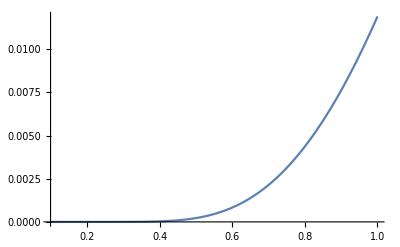

```mathematica
Plot[{Subscript[J, sub]/.{κ->1}},{T,0.1,1}]
```